```mathematica
SetDirectory[NotebookDirectory[]];
```

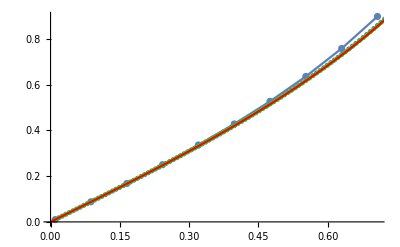

```mathematica
n10 = Import["./outputs/uloha3_10n.csv","CSV"];
n100 = Import["./outputs/uloha3_100n.csv","CSV"];
n1000 = Import["./outputs/uloha3_1000n.csv","CSV"];
DSolve[{x'[t]==x[t]*x[t]+1, x[0]==0},x,t];
Show[
ListPlot[n10],
ListLinePlot[n10],
ListPlot[n100],
ListLinePlot[n100],
ListPlot[n1000, PlotStyle->Green],
ListLinePlot[n1000, PlotStyle->Green],
Plot[Evaluate[x[t]/.%],{t,0,π/4}, PlotStyle->Red]
]
```